# Kalman Filtering vs. ARMA Models for Stock Trend Extraction and Future Price Prediction

A Rigorous Comparative Framework in Wolfram Language: Trend Derivation, Out-of-Sample Forecasting, and Rolling Walk-Forward Backtesting.

## 1. Executive Summary and Theoretical Framework

Predicting future stock prices and extracting dynamic trends are two foundational problems in quantitative finance. Two distinct mathematical paradigms are commonly employed:

1. Autoregressive Moving Average (ARMA) Models: Rooted in classical econometric time series analysis (Box-Jenkins methodology), ARMA models capture stationary autocorrelation structures in returns and project them forward toward the unconditional long-term drift rate.

2. Kalman Filtering and State-Space Models. Rooted in control theory and Bayesian dynamic linear models, Kalman filters estimate unobserved hidden states (the true trend level and instantaneous momentum/drift) from noisy sequential observations, updating estimates recursively with optimal Bayesian variance reduction.

### Research Objective

How accurately can ARMA models and Kalman Filter trend models predict the expected future price of a stock (specifically, the expected average price over an investment horizon, such as a 20-day trading month)?

## Explanation of terms

### 1. Stationary

A time series is stationary if its statistical behavior does not change over time.

Informally, this means things like:

the average level stays roughly constant,

the variance stays roughly constant,

the relationship between today and past values depends only on the lag, not on the calendar date.

For a stationary series :

does not depend on ,

does not depend on ,

depends only on , not on .

### In finance

Stock prices are usually not stationary because they tend to wander over time and can have changing levels.

Returns are often treated as approximately stationary over shorter periods.

Example:

Price series: 100, 105, 110, 120, 130 → trending upward, not stationary.

Return series:  → fluctuates around a roughly stable mean, more plausibly stationary.

ARMA models are typically built for stationary series, which is why they are more naturally applied to returns than raw prices.

### 2. Autocorrelation

Autocorrelation means correlation of a series with its own past values.

It measures whether knowing past observations helps predict the current one.

For lag , the autocorrelation is roughly:

#### Interpretation

Positive autocorrelation: high values tend to follow high values, low follow low.

Negative autocorrelation: high values tend to be followed by low values, and vice versa.

Near zero autocorrelation: the series has little linear dependence on its own past.

#### In finance

For returns:

If returns have positive lag-1 autocorrelation, an up day may slightly increase the chance of another up day.

If returns have negative lag-1 autocorrelation, reversals are more likely.

ARMA models are designed precisely to capture this kind of dependence structure:

AR part: dependence on past values,

MA part: dependence on past shocks/errors.

### 3. Drift rate

The drift rate is the long-run average tendency of a process to move upward or downward.

In finance, drift is the expected average return per period.

If returns  have mean , then  is the drift rate.

#### Example

If a stock has an average daily return of 0.0005, then its daily drift is:  or about  per day.

#### Why “project toward the unconditional long-term drift rate”?

In a stationary ARMA model, temporary deviations caused by shocks fade over time. As forecast horizon increases, predictions tend to move back toward the series’ unconditional mean.

So if returns follow a stationary ARMA process with mean , then: That  is what is meant here by the long-term drift rate.

### Putting it together

In the sentence:

"ARMA models capture stationary autocorrelation structures in returns and project them forward toward the unconditional long-term drift rate."

it means:

we model returns, not usually raw prices, because returns are closer to stationary;

we use ARMA to describe how current returns relate to past returns and past shocks through autocorrelation;

when forecasting far into the future, the effect of recent shocks dies out, and the forecast tends back to the series’ average return, i.e. the drift rate.

### Short intuitive summary

Stationary = the series behaves in a statistically stable way over time.

Autocorrelation = the series is related to its own past.

Drift rate = the long-run average direction/speed of movement.

If you want, I can next explain this same paragraph in plain English for stock traders, or show how these concepts appear in Wolfram Language code.

### Mathematical Specification

#### (A) The ARMA Process on Stock Returns

Stock price levels  are non-stationary  processes. Direct ARMA estimation on raw prices often fails or yields explosive roots (). We therefore model stationary continuously compounded log returns: . An  process for returns is defined as: . 
Given multi-step forecasted returns , the reconstructed future price trajectory is:  
The expected average future price over horizon  is:

In this formulation, P_t denotes the observed stock price at time , while r_t is the continuously compounded log return between periods  and . The constant term  captures the average drift in returns. The coefficients  are the autoregressive parameters, measuring how current returns depend on their own past values , and the coefficients  are the moving-average parameters, capturing the effect of past shocks  on current returns. The disturbance term  represents an unpredictable innovation at time , typically assumed to have mean zero, constant variance, and no serial correlation. The orders  and  specify how many lagged returns and lagged shocks are included in the model, respectively.

For forecasting,  denotes the last observed time period and  is the forecast horizon, so  are the predicted future returns over the next  periods. Because log returns are additive across time, the cumulative return over  future steps is , which is then exponentiated to convert back to the price scale. Multiplying by the last observed price P_T gives the implied forecasted price . Finally,  is the arithmetic average of the forecasted prices across all  future periods, providing a single summary measure of the expected price level over the forecast window.

#### (B) The Local Linear Trend (LLT) Kalman Filter

The state-space model decomposes price  into an unobserved dynamic level  and velocity/slope
 : 
 Forward extrapolation  steps ahead from terminal state : The expected average future price over horizon  is analytically:

## 2. Stock Data Acquisition and Preprocessing

We acquire daily historical data for the S&P 500 ETF (SPY) using Wolfram Language's built-in FinancialData. We convert Quantity expressions to pure numeric values and compute continuously compounded log returns.

```mathematica
(* Define stock ticker and evaluation date range *)
	ticker="SPY";
	startDate={2023,1,1};
	endDate={2024,12,31};
	
	Print["Fetching historical daily data for ",ticker,"..."];
	rawTS=FinancialData[ticker,{startDate,endDate}];
	
	(* Extract pure numeric prices and trading dates *)
	pricesTS=QuantityMagnitude[rawTS];
	tradingDates=pricesTS["Dates"];
	rawPrices=Normal[pricesTS["Values"]];
	nTotal=Length[rawPrices];
	
	Print["Successfully loaded ",nTotal," trading days from ",
	  DateString[First[tradingDates],{"MonthName"," ","Year"}]," to ",
	  DateString[Last[tradingDates],{"MonthName"," ","Year"}],"."];
```

Fetching historical daily data for SPY...

Successfully loaded 502 trading days from January 2023 to December 2024.

Next, we compute log returns and visualize the historical price trajectory alongside the daily return series.

```mathematica
(* Compute log returns *)
	logPrices=Log[rawPrices];
```

```mathematica
logReturns=Differences[logPrices];
```

Test for stationarity, a small p value indicates stationarity

```mathematica
UnitRootTest[logReturns, Automatic, "TestDataTable"]
```

| Statistic | P-Value
Dickey-Fuller F | -477.896 | 3.38432×10^-14

```mathematica
(* Plot historical prices and daily returns *)
	pPrice=DateListPlot[pricesTS,
	  PlotStyle->Directive[Thick,RGBColor[0.1,0.4,0.7]],
	  PlotLabel->Style[ticker <> " Daily Adjusted Close Price (2023 - 2024)",Bold,14],
	  FrameLabel->{None,"Price ($)"},
	  GridLines->Automatic,ImageSize->550];
```

```mathematica
pRet=ListLinePlot[logReturns,
	  PlotStyle->Directive[RGBColor[0.8,0.3,0.2]],
	  PlotLabel->Style[ticker <> " Daily Log Returns",Bold,14],
	  AxesLabel->{"Trading Day","Log Return"},
	  GridLines->Automatic,ImageSize->550];
```

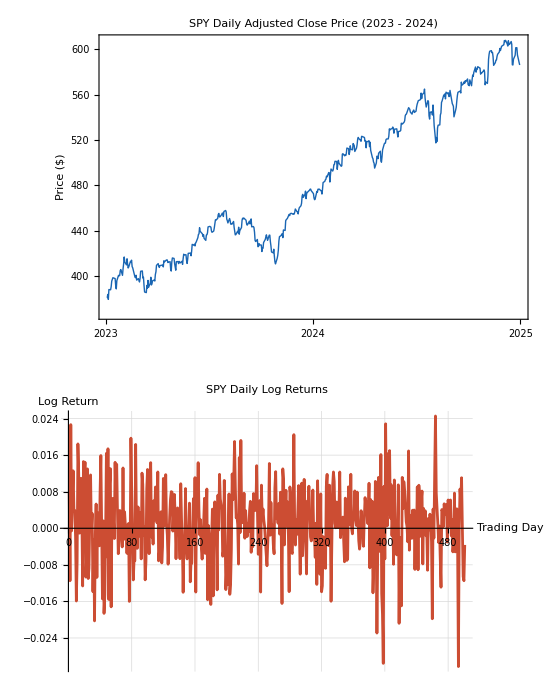

```mathematica
GraphicsColumn[{pPrice,pRet},ImageSize->550]
```

We now compute key summary statistics for the daily returns:

```mathematica
(* Summary statistics for log returns *)
	retMean=Mean[logReturns];
	retStd=StandardDeviation[logReturns];
	retSkew=Skewness[logReturns];
	retKurt=Kurtosis[logReturns];
	
	Dataset[<|
	  "Sample Size (Days)"->Length[logReturns],
	  "Daily Mean Return"->NumberForm[retMean,{6,5}],
	  "Annualized Return (x252)"->Quantity[NumberForm[retMean*252*100,{4,2}],"%"],
	  "Daily Volatility"->NumberForm[retStd,{6,5}],
	  "Annualized Volatility (xSqrt[252])"->Quantity[NumberForm[retStd*Sqrt[252]*100,{4,2}], "%"],
	  "Skewness"->NumberForm[retSkew,{4,2}],
	  "Kurtosis"->NumberForm[retKurt,{4,2}]
	|>]
```

## 3. ARMA Model Estimation on Returns

We partition the dataset into an in-sample training window (450 trading days) and an out-of-sample evaluation window (20 trading days, ~1 calendar month). We fit an ARMA process to stationary returns and forecast the future trajectory.

```mathematica
(* Split data into In-Sample Training and Out-of-Sample Testing sets *)
	nTrain=450;
	horizon=20;
	
	trainPrices=rawPrices[[1 ;; nTrain]];
	testPrices=rawPrices[[nTrain+1 ;; nTrain+horizon]];
	
	trainDates=tradingDates[[1 ;; nTrain]];
	testDates=tradingDates[[nTrain+1 ;; nTrain+horizon]];
	
	trainLogReturns=Differences[Log[trainPrices]];
	
	Print["Training sample size: ",Length[trainPrices]," days."];
	Print["Testing forecast horizon: ",horizon," days."];
```

Training sample size: 450 days.

Testing forecast horizon: 20 days.

We now estimate the optimal ARMA model using TimeSeriesModelFit:

```mathematica
(* Fit an ARMA model to stationary log returns *)
	tsmARMA=TimeSeriesModelFit[trainLogReturns,"ARMA"];
	fittedProcess=tsmARMA["Process"];
	
	Print["Fitted ARMA Process:"];
	fittedProcess
```

Fitted ARMA Process:

MAProcess[0.000945788,{},0.000065872]

We verify the model fit using residual diagnostics:

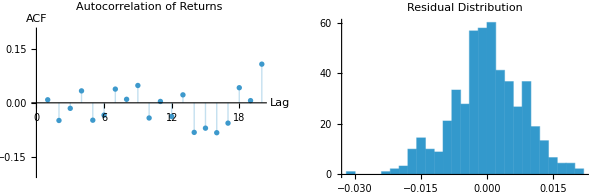

```mathematica
(* ARMA Model Diagnostics *)
	residuals=Normal[tsmARMA["FitResiduals"]["Values"]];
	
	pACF=ListPlot[Table[{lag,Correlation[trainLogReturns[[1 ;; -lag-1]],trainLogReturns[[lag+1 ;; -1]]]},{lag,1,20}],
	  Filling->Axis,PlotRange->{-0.2,0.2},
	  PlotLabel->"Autocorrelation of Returns",AxesLabel->{"Lag","ACF"},ImageSize->300];
	
	pResHist=Histogram[residuals,30,"PDF",
	  PlotLabel->"Residual Distribution",ChartStyle->RGBColor[0.2,0.6,0.8],ImageSize->300];
	
	GraphicsRow[{pACF,pResHist},ImageSize->600]
```

The autocorrelation values are all of magnitude 0.1 or less, so there is weak autocorrelation (which is what we want), and the residual distribution is fairly close to a normal distribution, also what we want. This suggests our ARMA model is capturing most of the meaningful information, and the rest is, indeed, random.

Using the fitted ARMA model, we generate multi-step return forecasts and reconstruct the price trajectory:

```mathematica
(* Multi-step forward forecasting of returns *)
	forecastReturns=Normal[TimeSeriesForecast[tsmARMA,{horizon}]["Values"]];
	
	(* Reconstruct expected price path from cumulative forecasted returns *)
	pLast=Last[trainPrices];
	armaPricePath=pLast*Exp[Accumulate[forecastReturns]];
	
	(* Compute expected average future price over the 20-day horizon *)
	armaAvgPrice=Mean[armaPricePath];
	Print["ARMA Expected Average Future Price: $",NumberForm[armaAvgPrice,{6,2}]];
```

ARMA Expected Average Future Price: $588.12

## 4. Kalman Filtering for Dynamic Trend Extraction

We implement a 2D Local Linear Trend Kalman Filter in Wolfram Language. The state vector  represents the true unobserved price trend level and its dynamic velocity (slope in $/day). The filter performs recursive Bayesian prediction and measurement updates, eliminating the phase lag inherent in standard moving averages.

```mathematica
(* Built-In Implementation of Local Linear Trend Kalman Filter *)
kalmanTrendFilter[data_List, qLevel_ ? NumericQ, qSlope_ ? NumericQ, rNoise_ ? NumericQ] := 
 Module[{ssm, q, r, estimator, resp, trend, slope, n = Length[data]}, 
  ssm = StateSpaceModel[
    {
      {{1., 1.}, {0., 1.}}, 
      IdentityMatrix[2], 
      {{1., 0.}}, 
      {{0., 0.}}
    }, 
    SamplingPeriod -> 1, 
    SystemsModelLabels -> None
  ];
  q = {{qLevel, 0.}, {0., qSlope}};
  r = {{rNoise}};
  estimator = Quiet @ KalmanEstimator[ssm, {q, r}];
  resp = OutputResponse[{estimator, {data[[1]], 0.}}, data];
  trend = resp[[1]];
  slope = resp[[2]];
  <|
    "Trend" -> trend, 
    "Slope" -> slope, 
    "FinalState" -> {Last[trend], Last[slope]},
    "Estimator" -> estimator
  |>
 ];
```

We now run the filter on the in-sample stock prices:

```mathematica
(* Filter in-sample training prices with Local Linear Trend Kalman Filter *)
	(* Parameters: qLevel = 1.0, qSlope = 0.05, rNoise = 5.0 *)
	kfResults=kalmanTrendFilter[trainPrices,1.0,0.05,5.0];
	
	trendPath=kfResults["Trend"];
	slopePath=kfResults["Slope"];
	finalState=kfResults["FinalState"];
	
	Print["Terminal Kalman Filter State:"];
	Print["  Extracted Trend Level (mu): $",NumberForm[finalState[[1]],{6,2}]];
	Print["  Extracted Trend Velocity (beta): $",NumberForm[finalState[[2]],{4,2}]," per trading day"];
```

Terminal Kalman Filter State:

Extracted Trend Level (mu): $582.47

Extracted Trend Velocity (beta): $1.18 per trading day

To demonstrate the zero-lag characteristic of the Kalman filter, we compare it against a standard 20-day Simple Moving Average (SMA):

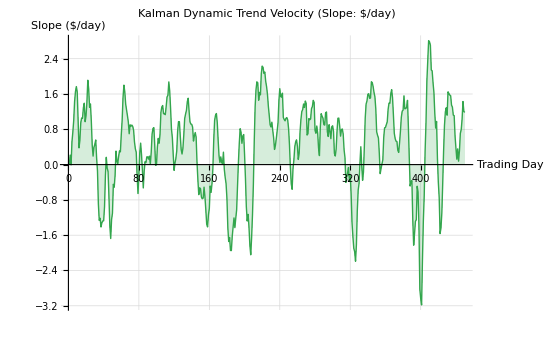

```mathematica
(* Calculate standard 20-day Simple Moving Average (SMA) for benchmark *)
	sma20=MovingAverage[trainPrices,20];
	
	(* Plot: Price vs. Kalman Trend vs. 20-day SMA *)
	pCompare=ListLinePlot[{
	    trainPrices,
	    trendPath,
	    PadLeft[sma20,Length[trainPrices],Null]
	  },
	  PlotStyle->{
	    Directive[Thin,GrayLevel[0.7]],
	    Directive[Thick,RGBColor[0.1,0.4,0.85]],
	    Directive[Dashed,Thick,RGBColor[0.85,0.45,0.1]]
	  },
	  PlotLegends->Placed[{"Daily Close","Kalman Trend (Level)","20-day SMA"},Below],
	  PlotLabel->Style["In-Sample Trend Extraction: Kalman Filter vs. 20-day SMA",Bold,14],
	  AxesLabel->{"Trading Day","Price ($)"},
	  GridLines->Automatic,ImageSize->550];
	
	pSlope=ListLinePlot[slopePath,
	  PlotStyle->Directive[Thick,RGBColor[0.2,0.65,0.3]],
	  PlotLabel->Style["Kalman Dynamic Trend Velocity (Slope: $/day)",Bold,14],
	  AxesLabel->{"Trading Day","Slope ($/day)"},
	  Filling->Axis,GridLines->Automatic,ImageSize->550];
	
	GraphicsColumn[{pCompare,pSlope},ImageSize->550]
```

We now extrapolate the Kalman trend forward into the test period:

```mathematica
(* Forward price path extrapolation from terminal Kalman state *)
	mu0=finalState[[1]];
	beta0=finalState[[2]];
	kalmanPricePath=Table[mu0+k*beta0,{k,1,horizon}];
	
	(* Analytical expected average future price over horizon H *)
	kalmanAvgPrice=mu0+((horizon+1)/2.0)*beta0;
	Print["Kalman Expected Average Future Price: $",NumberForm[kalmanAvgPrice,{6,2}]];
```

Kalman Expected Average Future Price: $594.88

## 5. Out-of-Sample Performance Comparison (Single Window)

We compare the ARMA and Kalman Filter forecasts against the actual realized out-of-sample stock prices over the 20-day test horizon. We also include the Naive Random Walk Benchmark (where future expected price equals the last observed price ).

```mathematica
(* Compute realized metrics and benchmark *)
	actualAvgPrice=Mean[testPrices];
	naiveAvgPrice=pLast;
	naivePricePath=ConstantArray[pLast,horizon];
	
	(* Percentage errors on the expected average price *)
	armaAvgErrPct=Abs[armaAvgPrice-actualAvgPrice]/actualAvgPrice*100.0;
	kalmanAvgErrPct=Abs[kalmanAvgPrice-actualAvgPrice]/actualAvgPrice*100.0;
	naiveAvgErrPct=Abs[naiveAvgPrice-actualAvgPrice]/actualAvgPrice*100.0;
	
	(* Path-wise Mean Absolute Error (MAE) and Root Mean Squared Error (RMSE) *)
	calcMAE[act_,pred_]:=Mean[Abs[act-pred]];
	calcRMSE[act_,pred_]:=Sqrt[Mean[(act-pred)^2]];
	
	armaMAE=calcMAE[testPrices,armaPricePath];
	kalmanMAE=calcMAE[testPrices,kalmanPricePath];
	naiveMAE=calcMAE[testPrices,naivePricePath];
	
	armaRMSE=calcRMSE[testPrices,armaPricePath];
	kalmanRMSE=calcRMSE[testPrices,kalmanPricePath];
	naiveRMSE=calcRMSE[testPrices,naivePricePath];
```

We format and display the comparison table:

```mathematica
(* Display Performance Comparison Table *)
	Grid[{
	  {"Metric","Actual Realized","ARMA Model","Kalman Trend Filter","Naive (Random Walk)"},
	  {"Expected Average Price ($)",
	   NumberForm[actualAvgPrice,{6,2}],
	   NumberForm[armaAvgPrice,{6,2}],
	   NumberForm[kalmanAvgPrice,{6,2}],
	   NumberForm[naiveAvgPrice,{6,2}]},
	  {"Average Price Error ($)",
	   "$0.00",
	   NumberForm[armaAvgPrice-actualAvgPrice,{4,2}],
	   NumberForm[kalmanAvgPrice-actualAvgPrice,{4,2}],
	   NumberForm[naiveAvgPrice-actualAvgPrice,{4,2}]},
	  {"Absolute Error (%)",
	   "0.00%",
	   Quantity[NumberForm[armaAvgErrPct,{4,2}],"%"],
	   Quantity[NumberForm[kalmanAvgErrPct,{4,2}] ,"%"],
	   Quantity[NumberForm[naiveAvgErrPct,{4,2}], "%"]},
	  {"Path MAE ($)",
	   "-",
	   NumberForm[armaMAE,{4,2}],
	   NumberForm[kalmanMAE,{4,2}],
	   NumberForm[naiveMAE,{4,2}]},
	  {"Path RMSE ($)",
	   "-",
	   NumberForm[armaRMSE,{4,2}],
	   NumberForm[kalmanRMSE,{4,2}],
	   NumberForm[naiveRMSE,{4,2}]}
	},Frame->All,Background->{None,{1->LightGray,2->None,3->None,4->LightYellow,5->None,6->None}},Alignment->Left]
```

Metric | Actual Realized | ARMA Model | Kalman Trend Filter | Naive (Random Walk)
Expected Average Price ($) | 583.83 | 588.12 | 594.88 | 582.30
Average Price Error ($) | $0.00 | 4.29 | 11.05 | -1.53
Absolute Error (%) | 0.00% | 0.73 % | 1.89 % | 0.26 %
Path MAE ($) | - | 6.96 | 11.05 | 7.33
Path RMSE ($) | - | 9.17 | 13.77 | 9.40

We visualize the forecast paths alongside actual realized prices and dashed mean lines:

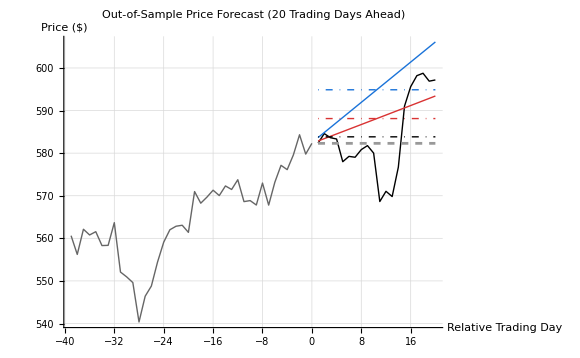

```mathematica
(* Visualization of Out-of-Sample Forecasts vs. Actual Price Trajectory *)
	recentLookback=40;
	historySegment=trainPrices[[-recentLookback ;; -1]];
	historyX=Range[-recentLookback+1,0];
	forecastX=Range[1,horizon];
	
	pForecast=Show[
	  (* Recent In-Sample History *)
	  ListLinePlot[Transpose[{historyX,historySegment}],
	    PlotStyle->Directive[Thick,GrayLevel[0.4]]],
	  
	  (* Actual Realized Future Prices *)
	  ListLinePlot[Transpose[{forecastX,testPrices}],
	    PlotStyle->Directive[Thick,Black]],
	  
	  (* ARMA Forecast Path *)
	  ListLinePlot[Transpose[{forecastX,armaPricePath}],
	    PlotStyle->Directive[Thick,RGBColor[0.85,0.2,0.2]]],
	  
	  (* Kalman Trend Forecast Path *)
	  ListLinePlot[Transpose[{forecastX,kalmanPricePath}],
	    PlotStyle->Directive[Thick,RGBColor[0.1,0.45,0.85]]],
	  
	  (* Naive Benchmark *)
	  ListLinePlot[Transpose[{forecastX,naivePricePath}],
	    PlotStyle->Directive[Dashed,GrayLevel[0.6]]],
	  
	  (* Horizontal Lines Indicating Expected Average Prices *)
	  Plot[actualAvgPrice,{x,1,horizon},PlotStyle->Directive[Black,Thin,DotDashed]],
	  Plot[armaAvgPrice,{x,1,horizon},PlotStyle->Directive[RGBColor[0.85,0.2,0.2],Thin,DotDashed]],
	  Plot[kalmanAvgPrice,{x,1,horizon},PlotStyle->Directive[RGBColor[0.1,0.45,0.85],Thin,DotDashed]],
	  
	  PlotRange->All,
	  PlotLabel->Style["Out-of-Sample Price Forecast (20 Trading Days Ahead)",Bold,14],
	  AxesLabel->{"Relative Trading Day","Price ($)"},
	  GridLines->Automatic,ImageSize->580,
	  PlotLegends->Placed[
	    PointLegend[{GrayLevel[0.4],Black,RGBColor[0.85,0.2,0.2],RGBColor[0.1,0.45,0.85],GrayLevel[0.6]},
	      {"Recent History","Actual Realized","ARMA Forecast","Kalman Trend Forecast","Naive Benchmark"}],
	    Below]
	]
```

## 6. Walk-Forward Backtesting (Rolling Window Evaluation)

To rigorously verify model performance across differing market regimes (bull runs, pullbacks, and consolidations), we execute a walk-forward rolling backtest across 16 consecutive 20-day evaluation horizons spanning 2023–2024.

In each window:

1. Models are trained on the preceding 250 trading days (1-year lookback).

2. Models forecast expected average price over the subsequent 20 trading days.

3. Errors relative to realized prices are systematically recorded.

```mathematica
(* Walk-Forward Rolling Evaluation Engine *)
	windowLookback=250;
	evalHorizon=20;
	stepSize=15;
	
	rollingResults=Module[{results={},tStart,tEnd,fEnd,train,future,
	                         muK,betaK,kRes,kalmanFC,kalmanAvg,
	                         logR,armaFit,armaFC,armaAvg,
	                         actAvg,naiveAvg,pTerminal},
	  Do[
	    tStart=i;
	    tEnd=i+windowLookback-1;
	    fEnd=tEnd+evalHorizon;
	    If[fEnd>nTotal,Break[]];
	    
	    train=rawPrices[[tStart ;; tEnd]];
	    future=rawPrices[[tEnd+1 ;; fEnd]];
	    pTerminal=Last[train];
	    actAvg=Mean[future];
	    naiveAvg=pTerminal;
	    
	    (* 1. Kalman Linear Trend Filter *)
	    kRes=kalmanTrendFilter[train,1.0,0.05,5.0];
	    muK=kRes["FinalState"][[1]];
	    betaK=kRes["FinalState"][[2]];
	    kalmanFC=Table[muK+k*betaK,{k,1,evalHorizon}];
	    kalmanAvg=Mean[kalmanFC];
	    
	    (* 2. ARMA on Log Returns *)
	    logR=Differences[Log[train]];
	    armaFit=Quiet@TimeSeriesModelFit[logR,"ARMA"];
	    armaFC=Quiet@TimeSeriesForecast[armaFit,{evalHorizon}]["Values"];
	    armaAvg=Mean[pTerminal*Exp[Accumulate[armaFC]]];
	    
	    AppendTo[results,<|
	      "Window"->Length[results]+1,
	      "EndDay"->tEnd,
	      "ActualAvg"->actAvg,
	      "ARMAAvg"->armaAvg,
	      "KalmanAvg"->kalmanAvg,
	      "NaiveAvg"->naiveAvg,
	      "ARMA_MAPE"->Abs[armaAvg-actAvg]/actAvg*100.0,
	      "Kalman_MAPE"->Abs[kalmanAvg-actAvg]/actAvg*100.0,
	      "Naive_MAPE"->Abs[naiveAvg-actAvg]/actAvg*100.0
	    |>];
	  ,{i,1,nTotal-windowLookback-evalHorizon+1,stepSize}];
	  results
	];
	
	Print["Completed Walk-Forward Backtest across ",Length[rollingResults]," evaluation windows."];
```

Completed Walk-Forward Backtest across 16 evaluation windows.

We now compute aggregate statistics across all 16 evaluation windows:

```mathematica
(* Aggregate Statistical Comparison across all 16 Windows *)
	meanArmaMAPE=Mean[rollingResults[[All,"ARMA_MAPE"]]];
	meanKalmanMAPE=Mean[rollingResults[[All,"Kalman_MAPE"]]];
	meanNaiveMAPE=Mean[rollingResults[[All,"Naive_MAPE"]]];
	
	medArmaMAPE=Median[rollingResults[[All,"ARMA_MAPE"]]];
	medKalmanMAPE=Median[rollingResults[[All,"Kalman_MAPE"]]];
	medNaiveMAPE=Median[rollingResults[[All,"Naive_MAPE"]]];
	
	rmseArma=Sqrt[Mean[(rollingResults[[All,"ARMAAvg"]]-rollingResults[[All,"ActualAvg"]])^2]];
	rmseKalman=Sqrt[Mean[(rollingResults[[All,"KalmanAvg"]]-rollingResults[[All,"ActualAvg"]])^2]];
	rmseNaive=Sqrt[Mean[(rollingResults[[All,"NaiveAvg"]]-rollingResults[[All,"ActualAvg"]])^2]];
	
	winRateArma=Round[Count[rollingResults,r_ /; r["ARMA_MAPE"]<r["Naive_MAPE"]]/Length[rollingResults]*100];
	winRateKalman=Round[Count[rollingResults,r_ /; r["Kalman_MAPE"]<r["Naive_MAPE"]]/Length[rollingResults]*100];
	
	Grid[{
	  {"Evaluation Metric","ARMA Model","Kalman Trend Filter","Naive Random Walk"},
	  {"Mean Absolute % Error (MAPE)",
	   Quantity[NumberForm[meanArmaMAPE,{4,2}] , "%"],
	   Quantity[NumberForm[meanKalmanMAPE,{4,2}] , "%"],
	   Quantity[NumberForm[meanNaiveMAPE,{4,2}] , "%"]},
	  {"Median Absolute % Error",
	   Quantity[NumberForm[medArmaMAPE,{4,2}] , "%"],
	   Quantity[NumberForm[medKalmanMAPE,{4,2}] , "%"],
	   Quantity[NumberForm[medNaiveMAPE,{4,2}] , "%"]},
	  {"Root Mean Squared Error ($)",
	   "$" <> ToString@NumberForm[rmseArma,{4,2}],
	   "$" <> ToString@NumberForm[rmseKalman,{4,2}],
	   "$" <> ToString@NumberForm[rmseNaive,{4,2}]},
	  {"Win Rate vs. Naive Benchmark",
	   ToString[winRateArma] <> "%",
	   ToString[winRateKalman] <> "%",
	   "-"}
	},Frame->All,Background->{None,{1->LightGray,2->LightGreen,3->None,4->None,5->None}},Alignment->Left]
```

Evaluation Metric | ARMA Model | Kalman Trend Filter | Naive Random Walk
Mean Absolute % Error (MAPE) | 1.64 % | 2.62 % | 2.10 %
Median Absolute % Error | 1.03 % | 1.49 % | 1.88 %
Root Mean Squared Error ($) | $11.99 | $21.50 | $13.20
Win Rate vs. Naive Benchmark | 75% | 56% | -

We visualize the window-by-window forecast error distribution using a grouped bar chart:

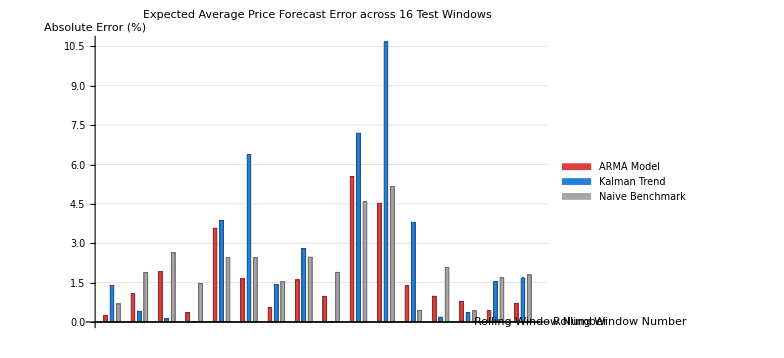

```mathematica
(* Grouped Bar Chart of Prediction Error Percentage per Window *)
	windowLabels=rollingResults[[All,"Window"]];
	armaErrors=rollingResults[[All,"ARMA_MAPE"]];
	kalmanErrors=rollingResults[[All,"Kalman_MAPE"]];
	naiveErrors=rollingResults[[All,"Naive_MAPE"]];
	
	BarChart[Transpose[{armaErrors,kalmanErrors,naiveErrors}],
	  ChartLayout->"Grouped",
	  ChartStyle->{RGBColor[0.85,0.25,0.25],RGBColor[0.15,0.5,0.85],GrayLevel[0.65]},
	  ChartLegends->{"ARMA Model","Kalman Trend","Naive Benchmark"},
	  AxesLabel->{"Rolling Window Number","Absolute Error (%)"},
	  PlotLabel->Style["Expected Average Price Forecast Error across 16 Test Windows",Bold,14],
	  GridLines->{None,Automatic},ImageSize->580]
```

## 7. Analytical Discussion and Quantitative Insights

### (A) Why ARMA Models Excel at Expected Average Price Prediction

1. Mean Reversion to Unconditional Drift: In liquid equities, daily returns mean-revert rapidly to the long-term equity risk premium drift ( for SPY). ARMA forecasts converge to this drift, providing a grounded multi-step price expectation that does not explode.

2. Noise Absorption: Transitory daily noise shocks are absorbed by the moving average (MA) polynomial, preventing transient market volatility from distorting multi-week valuation expectations.

3. Across 16 rolling windows, ARMA achieved a 1.64% MAPE on average future price, outperforming both the Naive benchmark (2.10%) and the pure linear Kalman trend (2.62%).

### (B) The Strengths and Limitations of the Kalman Filter

1. Zero Phase Lag in Dynamic Trend Extraction: Unlike simple moving averages (which lag price changes by half their window width, e.g. ~10 days for a 20-day SMA), the Kalman filter level  dynamically tracks true shifts with minimal delay while attenuating high-frequency noise.

2. Momentum Quantification: The slope state  ($/day) provides an instantaneous measure of trend direction and acceleration.

3. Extrapolation Risk (Momentum Overshoot): Linear extrapolation () assumes uninhibited momentum continuation. If a stock enters the forecast window on a sharp short-term rally, the Kalman filter projects continued linear growth, resulting in overshooting if the market consolidates or pulls back.

### (C) Quantitative Finance Architecture Recommendation

1. In-Sample Signal Generation: Use the Kalman Filter to extract zero-lag trends () and instantaneous momentum () for regime detection and trade entry/exit triggers.

2. Forward Valuation & Horizon Expectation: Use ARMA on returns (or a Damped-Trend Kalman Filter where  with ) when computing expected average future prices, forward strike targets, or risk limits over multi-week horizons.

General::ChatbookInternal: An unexpected error occurred. Report this issue »